# My glucose series

## Program

```mathematica
getTimeSer[gs_]:=Module[{tr},
tr=Transpose[gs];
TimeSeries[tr[[2]],{tr[[1]]}]]
```

```mathematica
getMarkPos[ser_]:=Position[ser,{_,_,{_String}}]
```

```mathematica
getMarkedDate[ser_]:=Module[{pos},
pos=Flatten[Position[ser,{_,_,{_String}}]];
Map[#[[1]]&,ser[[pos]]]
]
```

```mathematica
getMarkedItem[ser_]:=Module[{pos},
pos=Flatten[Position[ser,{_,_,{_String}}]];
ser[[pos]]
]
```

```mathematica
timeShift=2209021200
```

2209021200

```mathematica
(* createEpilog[gs_]:=Map[Text["*",{UnixTime[#]+timeShift,80}]&,getMarkedDate[gs]] *)
```

```mathematica
createEpilog[gs_]:=Map[Text[#[[3]],{UnixTime[#[[1]]]+timeShift,80}]&,getMarkedItem[gs]]
```

## Data

```mathematica
gs=Get["/Users/kouamano/Profile/blood-glc.txt"]
```

{{Thu 3 Feb 2022 06:05:00GMT+9,148,{}},{Thu 3 Feb 2022 11:16:00GMT+9,396,{}},{Thu 3 Feb 2022 16:31:00GMT+9,257,{}},{Fri 4 Feb 2022 06:06:00GMT+9,177,{}},{Fri 4 Feb 2022 11:16:00GMT+9,273,{}},{Fri 4 Feb 2022 18:30:00GMT+9,204,{}},{Sat 5 Feb 2022 05:57:00GMT+9,98,{}},{Sat 5 Feb 2022 12:15:00GMT+9,137,{}},{Sat 5 Feb 2022 17:15:00GMT+9,226,{}},{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Sun 6 Feb 2022 12:21:00GMT+9,374,{}},{Sun 6 Feb 2022 17:28:00GMT+9,241,{}},{Mon 7 Feb 2022 06:17:00GMT+9,158,{}},{Mon 7 Feb 2022 11:34:00GMT+9,293,{}},{Mon 7 Feb 2022 16:44:00GMT+9,382,{}},{Tue 8 Feb 2022 06:23:00GMT+9,152,{}},{Tue 8 Feb 2022 12:09:00GMT+9,399,{}},{Tue 8 Feb 2022 17:05:00GMT+9,275,{}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}},{Wed 9 Feb 2022 11:54:00GMT+9,348,{}},{Wed 9 Feb 2022 17:04:00GMT+9,271,{}},{Thu 10 Feb 2022 06:21:00GMT+9,216,{}},{Thu 10 Feb 2022 11:54:00GMT+9,133,{}},{Thu 10 Feb 2022 17:01:00GMT+9,264,{}},{Fri 11 Feb 2022 06:25:00GMT+9,191,{}},{Fri 11 Feb 2022 12:00:00GMT+9,197,{}},{Fri 11 Feb 2022 17:04:00GMT+9,224,{}},{Sat 12 Feb 2022 06:23:00GMT+9,165,{}},{Sat 12 Feb 2022 12:09:00GMT+9,210,{}},{Sat 12 Feb 2022 17:09:00GMT+9,213,{*}},{Sun 13 Feb 2022 06:17:00GMT+9,217,{}},{Sun 13 Feb 2022 12:27:00GMT+9,286,{}},{Sun 13 Feb 2022 17:23:00GMT+9,300,{}},{Mon 14 Feb 2022 06:12:00GMT+9,211,{}},{Mon 14 Feb 2022 12:18:00GMT+9,245,{}},{Mon 14 Feb 2022 18:49:00GMT+9,204,{}},{Tue 15 Feb 2022 06:18:00GMT+9,199,{}},{Tue 15 Feb 2022 11:59:00GMT+9,287,{}},{Tue 15 Feb 2022 18:21:00GMT+9,205,{}},{Wed 16 Feb 2022 06:15:00GMT+9,226,{}},{Wed 16 Feb 2022 12:16:00GMT+9,308,{}},{Wed 16 Feb 2022 18:27:00GMT+9,242,{}}}

```mathematica
getMarkPos[gs]
```

{{10},{19},{30}}

```mathematica
getMarkedDate[gs]
```

{Sun 6 Feb 2022 06:08:00GMT+9,Wed 9 Feb 2022 05:52:00GMT+9,Sat 12 Feb 2022 17:09:00GMT+9}

```mathematica
getMarkedItem[gs]
```

{{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}},{Sat 12 Feb 2022 17:09:00GMT+9,213,{*}}}

Basic points

```mathematica
startTime=UnixTime[gs[[1,1]]]+timeShift
endTime=UnixTime[gs[[-1,1]]]+timeShift
```

3852857100

3854024820

```mathematica
gts=getTimeSer[gs]
```

TimeSeries[…]

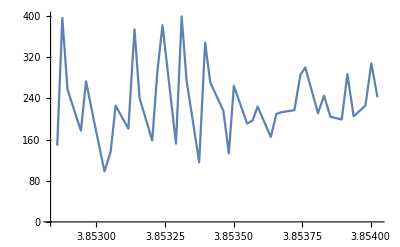

```mathematica
ListLinePlot[gts]
```

```mathematica
createEpilog[gs]
```

{Text[{*},{3853116480,80}],Text[{*},{3853374720,80}],Text[{*},{3853674540,80}]}

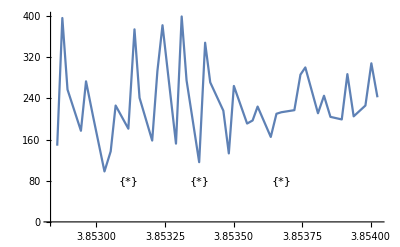

```mathematica
ListLinePlot[gts,Epilog->createEpilog[gs]]
```

Shift

```mathematica
1643835900-3852857100
```

-2209021200

Interpolation

```mathematica
Interpolation[gts]
```

InterpolatingFunction[…]

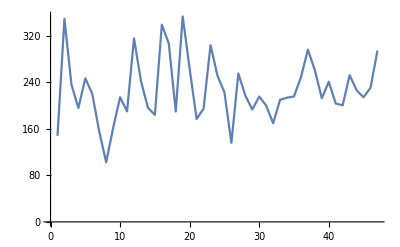

```mathematica
ListLinePlot[Table[Interpolation[gts][t],{t,startTime,endTime,25000}]]
```

Fourier(1)

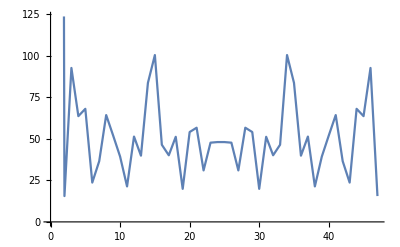

```mathematica
ListLinePlot[Fourier[Table[Interpolation[gts][t],{t,startTime,endTime,25000}]]//Abs]
```

Fourier(2)

```mathematica
Range[startTime,endTime,28000]//Length
```

42

InterpolatingFunction::dmval: 入力値{3853697100}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{3853725100}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{3853753100}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

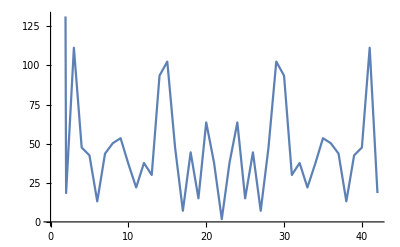

```mathematica
ListPlot[Fourier[InterpolatingFunction[…][Range[startTime,endTime,28000]]//N]//Abs,Joined->True]
```